```mathematica
XX = 2Sum[Sum[x^(l-k) ,{k,n,l-1}],{l,n,m-1}] + Sum[1 ,{l,n,m-1}]
```

m-n+(2 x (-1+m+n (-1+x)-m x+x^(m-n)))/(-1+x)^2

```mathematica
Snm=(XX/.x->Cos[β])//FullSimplify
```

m-n+(2 Cos[β] (-1+m-n+(-m+n) Cos[β]+Cos[β]^(m-n)))/(-1+Cos[β])^2

```mathematica
Anm = Sum[Cos[β]^(k-1),{k,n,m-1}]
```

((Cos[β]^m-Cos[β]^n) Sec[β])/(-1+Cos[β])

```mathematica
Rnm=FullSimplify[Snm/Anm^2 -1]
```

-1+(Cos[β]^2 (m-n+Cos[β] (-2+(-m+n) Cos[β]+2 Cos[β]^(m-n))))/((Cos[β]^m-Cos[β]^n)^2)

```mathematica
F[x_, y_, β_ ] =Rnm/.{ m->x/β^2, n->y/β^2}
```

-1+(Cos[β]^2 (x/β^2-y/β^2+Cos[β] (-2+(-x/β^2+y/β^2) Cos[β]+2 Cos[β]^(x/β^2-y/β^2))))/((Cos[β]^(x/β^2)-Cos[β]^(y/β^2))^2)

```mathematica
FullSimplify[Normal[Series[F[x,y,β],{β ,0,1},Direction->1]],{0 < y < x }]
```

-1+(-2+2 ⅇ^(1/2 (-x+y))+x-y)/((ⅇ^(-x/2)-ⅇ^(-y/2))^2)

```mathematica
FindMinimum[-1+(-2+2 ⅇ^(1/2 (-x+y))+x-y)/((ⅇ^(-x/2)-ⅇ^(-y/2))^2),{x,0,1},{y,0,x}]
```

FindMinimum::srect: Value x in search specification {y,0,x} is not a number or array of numbers.

FindMinimum[-1+(-2+2 ⅇ^(1/2 (-x+y))+x-y)/((ⅇ^(-x/2)-ⅇ^(-y/2))^2),{x,0,1},{y,0,x}]

```mathematica
Plot3D[-1+(-2+2 ⅇ^(1/2 (-x+y))+x-y)/((ⅇ^(-x/2)-ⅇ^(-y/2))^2),{x,0.0001,7},{y,0.0001,x-0.0001},PlotRange->All]
```

-Graphics3D-

```mathematica
Plus @@ Range[10]
```

55

```mathematica
H[q_] :=
Block[{pp},
pp = Select[Range[q-1],GCD[#,q]==1&];
(Plus @@( Cot[Pi N[ pp/q]]^2))
]
```

```mathematica
H[17]
```

80.

```mathematica
Hdata = {ParallelTable[{x,H[x]},{x,10000,20000,2}],ParallelTable[{x,H[x]},{x,10001,20001,2}]};
```

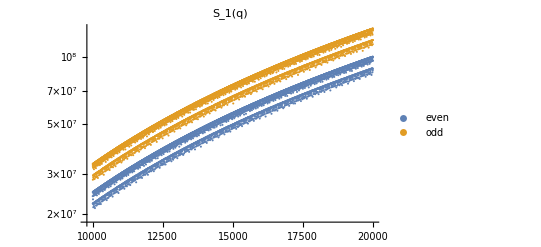

```mathematica
ListLogPlot[Hdata,PlotLegends->{"even","odd"}, PlotLabel->"S_1(q)"]
```

```mathematica
H2[q_] :=
Block[{rats},
rats = N[Select[Range[q-1],GCD[#,q]==1&]/q];
(Plus @@( Cot[Pi rats]^2 Cos[2 Pi rats]))
]
```

```mathematica
H2data = {ParallelTable[{x,H2[x]},{x,10000,20000,2}],ParallelTable[{x,H2[x]},{x,10001,20001,2}]};
```

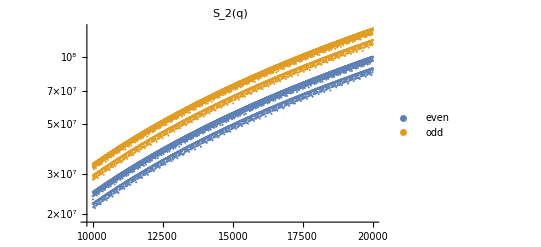

```mathematica
ListLogPlot[H2data,PlotLegends->{"even","odd"}, PlotLabel->"S_2(q)"]
```

```mathematica
ClearAll[Num, Den];
```

```mathematica
Den[M_, N_] := Sum[EulerPhi[q]Sum[If[Mod[N+ q r,2]==0,Binomial[N,(N+q r)/2],0]2^(-N),{r,-Floor[N/q],Floor[N/q]}],{q,2 + Mod[N,2],M-2}];
```

```mathematica
{N[Den[100, 100]],N[Den[101, 101]]}
```

{241.27,7.03851}

```mathematica
entropydata = With[{N = 5000}, ParallelTable[{n,Log[Den[n,n]]},{n,N/2,N}]];
```

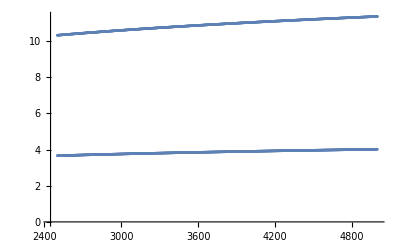

```mathematica
ListPlot[entropydata]
```

```mathematica
GetEvenStep[list_]:=Partition[list,2][[All,1]];

GetOddStep[list_]:=Partition[list,2][[All,2]];
```

```mathematica
entropyEvendata = GetEvenStep[entropydata];
```

```mathematica
Dimensions[entropyEvendata]
```

{1250,2}

```mathematica
emodelEven = LinearModelFit[entropyEvendata,{ Log[x]},x]
```

FittedModel[-1.4177+1.50012 Log[x]]

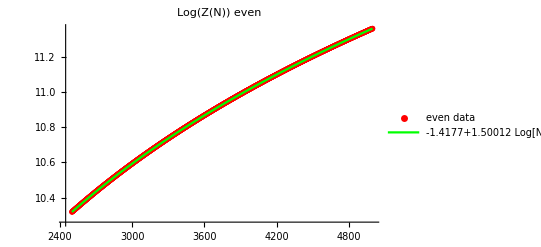

```mathematica
EntropyEvenPlot =Show[
ListPlot[entropyEvendata, PlotStyle->{Red, PointSize[0.01]},
PlotLegends->{"even data"}],
Plot[emodelEven[x],{x,entropyEvendata[[1,1]],entropyEvendata[[-1,1]]},PlotStyle->{Green, Thick},
PlotLegends->{emodelEven[N]},PlotRange->All],
PlotLabel->"Log(Z(N)) even"
]
```

```mathematica
emodelEven["ParameterTable"]
```

General::munfl: Exp[-7396.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-10095.3] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.4177 | 0.000107334 | -13208.3 | 0.
Log[x] | 1.50012 | 0.0000130697 | 114778. | 0.

```mathematica
entropyOdddata = GetOddStep[entropydata];
```

```mathematica
emodelOdd = LinearModelFit[entropyOdddata,{Log[x]},x]
```

FittedModel[-0.334062+0.51064 Log[x]]

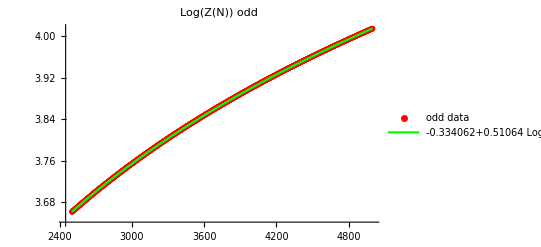

```mathematica
EntropyOddPlot =Show[
ListPlot[entropyOdddata, PlotStyle->{Red, PointSize[0.01]},
PlotLegends->{"odd data"}],
Plot[emodelOdd[x],{x,entropyOdddata[[1,1]],entropyOdddata[[-1,1]]},PlotStyle->{Green, Thick},
PlotLegends->{emodelOdd[N]},PlotRange->All],
PlotLabel->"Log(Z(N)) odd"
]
```

```mathematica
emodelOdd["ParameterTable"]
```

General::munfl: Exp[-5531.53] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8688.91] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.334062 | 0.000112756 | -2962.69 | 0.
Log[x] | 0.51064 | 0.0000137295 | 37193. | 0.

```mathematica
ht =ParallelTable[H[q],{q,2,10000,2}];
```

```mathematica
zh = Accumulate[ht];
```

```mathematica
Dimensions[zh]
```

{5000}

```mathematica
qq = Range[2,10000,2];
```

```mathematica
qq[[-1]]
```

10000

```mathematica
bb = Table[q(q-1)/32Binomial[q,q/2]2^(-q),{q,2,10000,2}];
```

```mathematica
Dimensions[bb]
```

{5000}

```mathematica
evenZdata = Exp[emodelEven /@qq];
```

```mathematica
evenZdata[[10]]
```

21.677

```mathematica
test = zh *bb /evenZdata;
```

```mathematica
test[[1]]
```

1.70974×10^-34

```mathematica
xx = Range[2,10000,2][[-1000;;]];
```

```mathematica
data1 =Transpose[{xx,test[[-1000;;]]}];
```

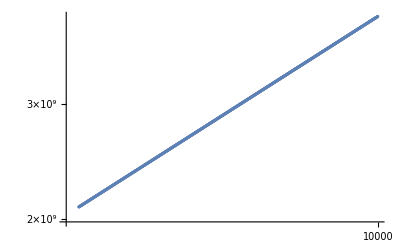

```mathematica
ListLogLogPlot[data1]
```

```mathematica
s1model = LinearModelFit[Log[data1],{ x},x]
```

FittedModel[-5.5033+2.99997 x]

```mathematica
s1model["ParameterTable"]
```

General::munfl: Exp[-7427.13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9025.81] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -5.5033 | 0.000102479 | -53701.9 | 0.
x | 2.99997 | 0.0000112574 | 266490. | 0.

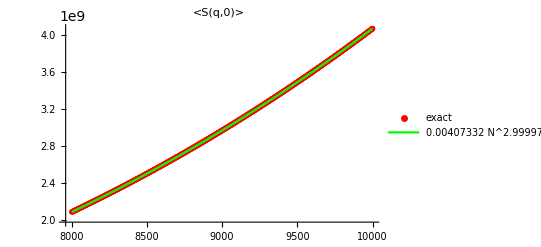

```mathematica
S1Plot =Show[
ListPlot[data1, PlotStyle->{Red, PointSize[0.01]},
PlotLegends->{"exact"}],
Plot[Exp[s1model[Log[x]]],{x,xx[[1]],xx[[-1]]},PlotStyle->{Green, Thick},
PlotLegends->{Exp[s1model[Log[N]]]},PlotRange->All],
PlotLabel->"<S(q,0)>"
]
```

```mathematica
ht2 =ParallelTable[H2[q],{q,2,10000,2}];
```

```mathematica
zh2= Accumulate[ht2];
```

```mathematica
Dimensions[zh2]
```

{5000}

```mathematica
test2 = zh2 *bb/evenZdata;
test2[[-1]]
```

4.07133×10^9

```mathematica
data2 =Transpose[{xx,test2[[-1000;;]]}];
```

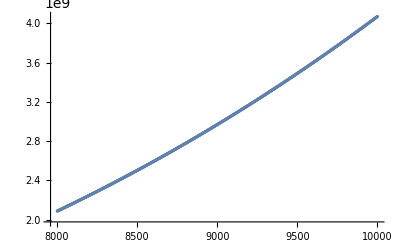

```mathematica
ListPlot[data2]
```

```mathematica
s2model = LinearModelFit[Log[data2],{x},x]
```

FittedModel[-5.50619+3.00026 x]

```mathematica
s2model["ParameterTable"]
```

General::munfl: Exp[-7427.69] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9025.94] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -5.50619 | 0.000102475 | -53731.9 | 0.
x | 3.00026 | 0.000011257 | 266524. | 0.

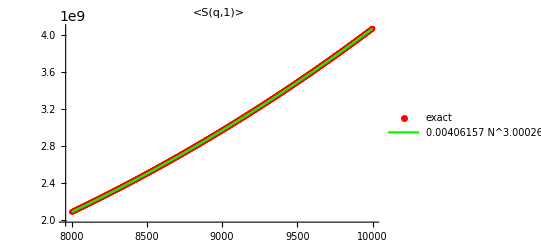

```mathematica
S2Plot =Show[
ListPlot[data2, PlotStyle->{Red, PointSize[0.01]},
PlotLegends->{"exact"}],
Plot[Exp[s2model[Log[x]]],{x,xx[[1]],xx[[-1]]},PlotStyle->{Green, Thick},
PlotLegends->{Exp[s2model[Log[N]]]},PlotRange->All],
PlotLabel->"<S(q,1)>"
]
```

```mathematica
(* old stuff below*)
```

```mathematica
ProbQdata = Block[{M = 1000, DNN, x},
DNN=N[Den[M,M]];
 ParallelTable[{x/M,N[Den[x,M]]/DNN},{x,2,M}]
];
```

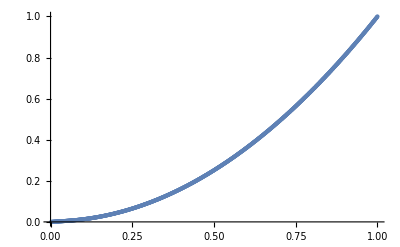

```mathematica
ListPlot[ProbQdata]
```

```mathematica
ProbQdataE =GetEvenStep[ProbQdata];
```

```mathematica
PQmodelEven = LinearModelFit[ProbQdataE,{x^2},x]
```

FittedModel[0.00235669+0.996704 x^2]

```mathematica
ProbQdataO=GetOddStep[ProbQdata];
```

```mathematica
PQmodelOdd= LinearModelFit[ProbQdataO,{x^2},x]
```

FittedModel[0.00248149+0.997335 x^2]

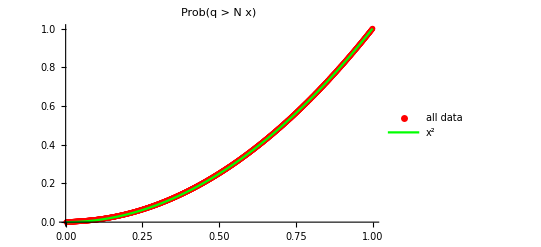

```mathematica
ProbQPlot =Show[
ListPlot[ProbQdata, PlotStyle->{Red, PointSize[0.01]},
PlotLegends->{"all data"}],
Plot[x^2,{x,0,1},PlotStyle->{Green, Thick},
PlotLegends->{x^2},PlotRange->All],
PlotLabel->"Prob(q > N x)"
]
```

```mathematica
qq = Range[2,10000,2];
```

```mathematica
ht2 =ParallelTable[H2[q],{q,2,10000,2}];
```

```mathematica
zh2= Accumulate[ht2];
```

```mathematica
dd = EulerPhi /@ qq;
```

```mathematica
dds = Accumulate[dd];
```

```mathematica
Avh2 = Transpose[{qq,zh2/dds}];
```

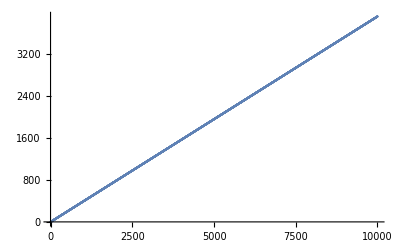

```mathematica
ListPlot[Avh2]
```

```mathematica
hmodelEven = LinearModelFit[Avh2,{x}, x]
```

FittedModel[-1.61993+0.390982 x]

```mathematica
hmodelEven["ParameterTable"]
```

General::munfl: Exp[-8534.15] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-44634.6] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.61993 | 0.00422857 | -383.091 | 0.
x | 0.390982 | 7.323×10^-7 | 533910. | 0.

```mathematica
Oqq = Range[3,10000,2];
```

```mathematica
Oht2 =ParallelTable[H2[q],{q,3,10000,2}];
```

```mathematica
zh2= Accumulate[ht2];
```

```mathematica
dd = EulerPhi /@ qq;
```

```mathematica
dds = Accumulate[dd];
```

```mathematica
Avh2 = Transpose[{qq,zh2/dds}];
```

```mathematica
ListPlot[Avh2]
```

-Graphics-

```mathematica
hmodelEven = LinearModelFit[Avh2,{x}, x]
```

FittedModel[-1.61993+0.390982 x]

```mathematica
hmodelEven["ParameterTable"]
```

General::munfl: Exp[-8534.15] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-44634.6] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.61993 | 0.00422857 | -383.091 | 0.
x | 0.390982 | 7.323×10^-7 | 533910. | 0.